```mathematica
path=NotebookDirectory[]
```

/home/mr/Desktop/TMDICE/test/

```mathematica
(*Put here the name of the file created by execution of the "demo.out" file, then evaluate the Notebook, by clicking in the upper index panel on "Evaluation", then "Evaluate Notebook"*)
```

```mathematica
filename="testfile";
```

```mathematica
indata=Import[path<>filename,"Table"];
```

```mathematica
indatawithouthead=Drop[indata,Position[indata,{"Index","for","event","x","kt","phik","typ"}][[1]][[1]]];
seplist=Flatten[Position[indatawithouthead,{"new","event"}]];
seplist=Insert[seplist,0,1];
eventlist={};
For[i=1,i<Length[seplist],i++,
event={};
For[j=seplist[[i]]+1,j≤seplist[[i+1]]-1,j++,AppendTo[event,indatawithouthead[[j]]] ];
AppendTo[eventlist,event];]
```

```mathematica
(*This is the first event*)
```

```mathematica
eventlist[[1]]
```

{{0,1,0.445144,1.67863,1}}

```mathematica
Nevents=Length[eventlist]
```

100000

```mathematica
(*list of gluon and quark/antiquark (singlet) x and kt is being extracted:*)
```

```mathematica
(*List of gluons*)
```

```mathematica
gluonflavorlist=Position[eventlist,2];
gluonlist={};
For[i=1,i≤Length[gluonflavorlist],i++,
If[gluonflavorlist⟦i⟧⟦3⟧==5,AppendTo[gluonlist,eventlist⟦gluonflavorlist⟦i⟧⟦1⟧⟧⟦gluonflavorlist⟦i⟧⟦2⟧⟧]]]
gluonlist=Drop[gluonlist,None,1];
gluonlist=Drop[gluonlist,None,-2];
```

```mathematica
(*List of quarks*)
```

```mathematica
quarkflavorlist=Position[eventlist,1];
quarklist={};
For[i=1,i≤Length[quarkflavorlist],i++,
If[quarkflavorlist⟦i⟧⟦3⟧==5,AppendTo[quarklist,eventlist⟦quarkflavorlist⟦i⟧⟦1⟧⟧⟦quarkflavorlist⟦i⟧⟦2⟧⟧]]]
quarklist=Drop[quarklist,None,1];
quarklist=Drop[quarklist,None,-2];
```

```mathematica
(*List of antiquarks*)
```

```mathematica
antiquarkflavorlist=Position[eventlist,-1];
antiquarklist={};
For[i=1,i≤Length[antiquarkflavorlist],i++,
If[antiquarkflavorlist⟦i⟧⟦3⟧==5,AppendTo[antiquarklist,eventlist⟦antiquarkflavorlist⟦i⟧⟦1⟧⟧⟦antiquarkflavorlist⟦i⟧⟦2⟧⟧]]]
antiquarklist=Drop[antiquarklist,None,1];
antiquarklist=Drop[antiquarklist,None,-2];
```

```mathematica
(*singlet*)
```

```mathematica
singletlist=Join[quarklist,antiquarklist];
(*Here the resulting fragmentation functions for gluons, first the fragmentation function over variables x and transverse momentum kt, then the integrated fragmentation functions, first over x, then over kt*)
```

```mathematica
Histogram3D[ WeightedData[gluonlist,(1./0.02)*(20/15)*(1/Nevents)*Flatten[Drop[gluonlist,None,-1]]],{{0,1,0.02},{0,15,15/20}},PlotRange->{{0,1},{0,15},All},AxesLabel->{"x","k_T","D̃(x,k_T)"}]
```

-Graphics3D-

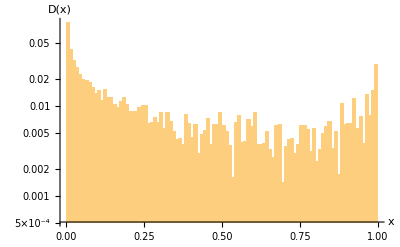

```mathematica
Histogram[ WeightedData[Flatten[Drop[gluonlist,None,-1]],100./Nevents*Flatten[Drop[gluonlist,None,-1]]],{0.,1.,1./100.},PlotRange->{{0,1},All},ScalingFunctions->"Log",AxesLabel->{"x","D(x)"}]
```

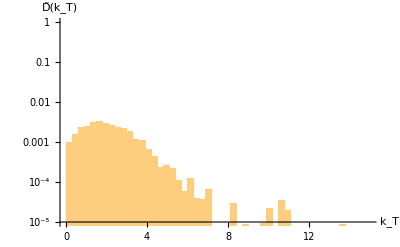

```mathematica
Histogram[ WeightedData[Flatten[Drop[gluonlist,None,1]],(50/15)*(1/Nevents)*Flatten[Drop[gluonlist,None,-1]]],{0.,15.,15./50.},PlotRange->{{0,15},{0.00001,1}},ScalingFunctions->"Log",AxesLabel->{"k_T","D̃(k_T)"}]
```

```mathematica
(*Here the resulting fragmentation functions for the singlets, first the fragmentation function over variables x and transverse momentum kt, then the integrated fragmentation functions, first over x, then over kt*)
```

```mathematica
Histogram3D[ WeightedData[singletlist,(1./0.02)*(20/15)*(1/Nevents)*Flatten[Drop[singletlist,None,-1]]],{{0,1,0.02},{0,15,15/20}},PlotRange->{{0,1},{0,15},All},AxesLabel->{"x","k_T","D̃(x,k_T)"}]
```

-Graphics3D-

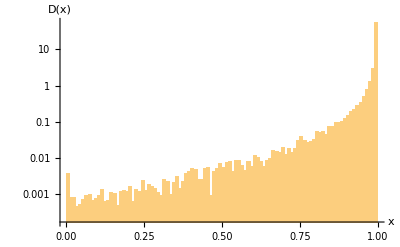

```mathematica
Histogram[ WeightedData[Flatten[Drop[singletlist,None,-1]],100./Nevents*Flatten[Drop[singletlist,None,-1]]],{0.,1.,1./100.},PlotRange->{{0,1},All},ScalingFunctions->"Log",AxesLabel->{"x","D(x)"}]
```

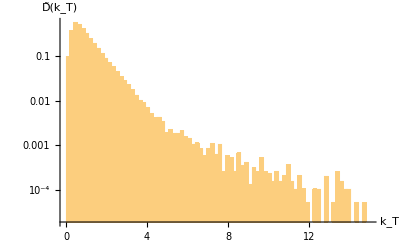

```mathematica
Histogram[ WeightedData[Flatten[Drop[singletlist,None,1]],(80/15)*(1/Nevents)*Flatten[Drop[singletlist,None,-1]]],{0,15,15./80.},PlotRange->{{0,15},All},ScalingFunctions->"Log",AxesLabel->{"k_T","D̃(k_T)"}]
```